## 3.029 Spring 2022 Lecture 12 - 03/09/2022

## Step-Growth Polymerization

Last lecture, we developed a reptation model for a single polymer chain

Today, we will investigate the collision-free reptation of multiple chains

And use it to investigate step-growth polymerization

## Initialization Functions from L10

Making a 2D correlated polymer

```mathematica
angularRange[correlation_]:={-1,1}(1-correlation)2π/3

collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]["Distance"]<bondLength

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{

nf=Nearest[chainSoFar->All],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision

},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]/;Length[chainSoFar]>1

correlatedPolymerChain2D[numberUnits_,correlation_]:=AnglePath[RandomReal[angularRange[correlation],numberUnits-1]]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]
```

Single chain reptation

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]

moveSingleChain[ positions_,ds_,stickiness_:0.1]:= 
Block[{newPositions},
newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];
If[collisionFreeQ[newPositions],newPositions,positions]
]

displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },

Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];

newPositions/@Range[Length[Δ]]
]

precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

## Multiple Chains Reptating

We wish to extend our single-chain reptation to multiple chains

But we similarly have to be concerned about collisions

We will use a hierarchical collision-detection!

We’ll use the following polymer chain to develop our collision detection

Note the functions to make this are from L10 (see collapsed section above)

```mathematica
SeedRandom[1111];
chainPositions=collisionFreeCorrelatedPolymerChain2D[12,0.4];
```

First, we start by checking if the axis-aligned bounding boxes of two chains overlap

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

pairWiseAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)&&(yMaxA>yMinB&&yMinA<yMaxB)
```

Let’s define a new visualization function to help us with debugging bounding boxes collisions

```mathematica
chainGraphic[positions_,bb_,col_:RandomColor[]]:= {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[None],EdgeForm[col//Darker],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}
```

We construct the bounding box for our polymer chain

and check whether it intersects with the bounding box of another chain

for simplicity, we use the same chain - just translated

True

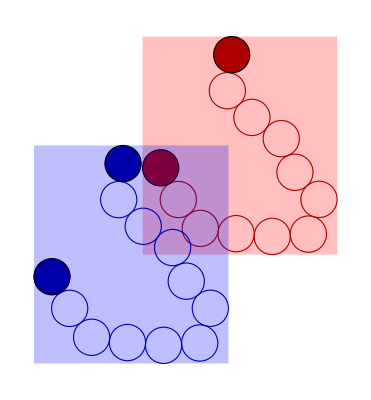

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

pairWiseAxesAlignedIntersection[bbA,bbB]//Echo;

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}]]

]
```

Great, our bounding-box collision detection seems to work!

Next, we only keep points on each chain inside the overlap region

```mathematica
returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[pos,xMax>#[[1]]>xMin&&yMax>#[[2]]>yMin&],{pos,{positionsA,positionsB}}]
]
```

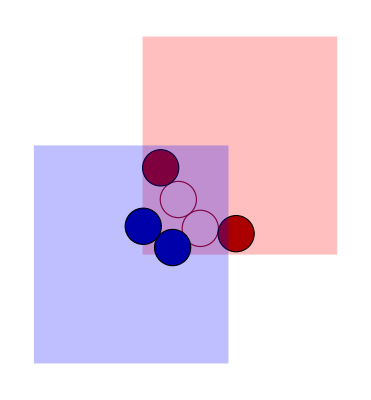

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}]]

]
```

This again seems to work well, and reduces the problem considerably

Quick note: Later, we will concern ourselves with the exact position of collisions

To check e.g. if an end-mer collided with another end-mer

As such, we’ll need to update this function later to also return the indices of the selected points

If the two chains are non-empty, we finally check pairwise distances

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB,dm},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];

MatrixForm[
dm=DistanceMatrix[posA,posB]
]//Echo;

Min[dm]<1

]
```

(2.22098 | 1.68108
1.33284 | 1.21777
0.928771 | 1.57581
1.79453 | 2.57211)

True

Remember our discussion on checking pairwise distances last lecture

We can do a little faster by looping over a Nearest function until we find the first distance less than 1

```mathematica
shortestDistanceLessThanOne[posA_,posB_]:=Block[{nf=Nearest[posA->"Distance"],i=1,d=2.,l=Length[posB]},
While[d>1. && i<=l,
d=First[nf[posB[[i]]]];
i++
];
d<1.
]
```

```mathematica
Block[{posA=chainPositions,posB=TranslationTransform[{-3,-3}]@chainPositions,bbA,bbB,dm},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];

shortestDistanceLessThanOne[posA,posB]

]
```

True

The final piece we need is a connectivity matrix telling us which bounding boxes overlap

We’ll construct this by looking at the upper-triangle part of the matrix at each step

```mathematica
Subsets[Range[6],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

```mathematica
MatrixForm[SparseArray[Subsets[Range[6],{2}]->1]]
```

(0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1)

Is this efficient? How can we do better?

```mathematica
Clear[connectivityMatrixIndex,connectivityMatrix]

connectivityMatrixIndex[bbs_,{i_,j_}]:=pairWiseAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],is},
SparseArray[s->(connectivityMatrixIndex[bbs,#]&/@s),{l,l}]
]
```

Connectivity Matrix  (0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

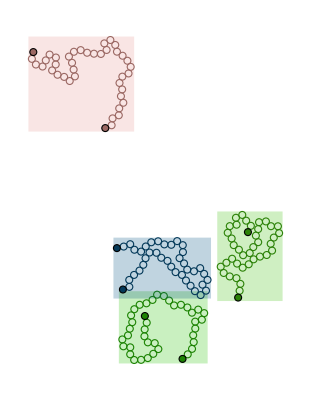

```mathematica
(*SeedRandom[1111];*)
SeedRandom[11111];
listOfPositions=Table[collisionFreeCorrelatedPolymerChain2D[40,0.3,RandomReal[{-30,30},2]],4];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
cols=RandomColor[4];
Echo[MatrixForm[connectivityMatrix[bbs]],"Connectivity Matrix"];
graphicMultiple=Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]]
```

Wrapping it all together

```mathematica
pairwiseChainCollisionQ[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,False,shortestDistanceLessThanOne[posA,posB]]
]

collisionsFreeChainsQ[listOfPositions_]:=Block[{
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero},

mij=connectivityMatrix[bbs];
nonzero=mij["NonzeroPositions"];


NoneTrue[nonzero,pairwiseChainCollisionQ[{listOfPositions,bbs},#]&]

]

moveAllChains[listOfPositions_,ds_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds]&/@listOfPos;
If[collisionsFreeChainsQ[listOfPos],listOfPos,listOfPositions]
]
```

```mathematica
Dynamic[Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]]]
```

```mathematica
Do[
listOfPositions=moveAllChains[listOfPositions,.1];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
Pause[0.01],
{1000}]
```

$Aborted

## Step-Growth Polymerization